{a (-c+s),b r-c k s,(-1+r) s}

{{r→1,c→-(√b)/(√k),s→-(√b)/(√k)},{r→1,c→(√b)/(√k),s→(√b)/(√k)},{r→0,c→0,s→0}}

(0 | -a | a
b | -k s | -c k
s | 0 | -1+r)

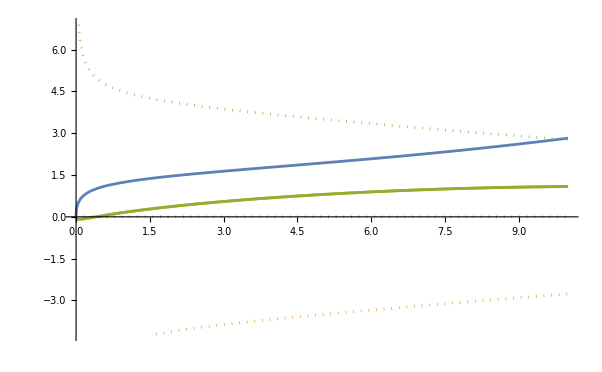

```mathematica
{
a(s-c),
b r-k c s,
s(r-1)
}
Solve[Map[#==0&,%],{r,c,s}]
Grad[%%,{r,c,s}];
%//MatrixForm
ReImPlot[Evaluate[%%/.%%%[[1]]/.{a->5,b->2.5}//Eigenvalues],{k,0,10}]
```

{a (-c+s),b r-c k s,(-1+r) s}

{{r→1,c→-(√b)/(√k),s→-(√b)/(√k)},{r→1,c→(√b)/(√k),s→(√b)/(√k)},{r→0,c→0,s→0}}

(0 | -a | a
b | -k s | -c k
s | 0 | -1+r)

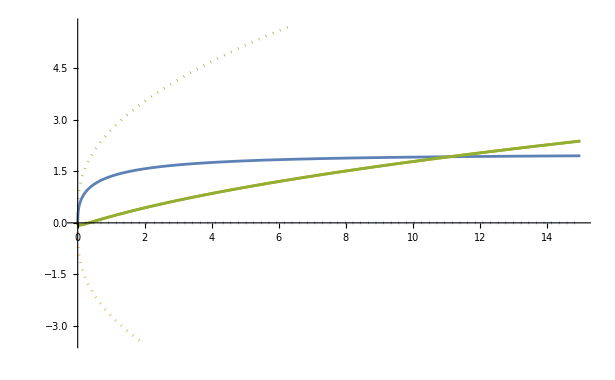

```mathematica
{
a(s-c),
b r-k c s,
s(r-1)
}
Solve[Map[#==0&,%],{r,c,s}]
Grad[%%,{r,c,s}];
%//MatrixForm
ReImPlot[Evaluate[%%/.%%%[[1]]/.{a->5,k->3}//Eigenvalues],{b,0,15}]
```

{a (-c+s),b r-c k s,(-1+r) s}

{{r→1,c→-(√b)/(√k),s→-(√b)/(√k)},{r→1,c→(√b)/(√k),s→(√b)/(√k)},{r→0,c→0,s→0}}

(0 | -a | a
b | -k s | -c k
s | 0 | -1+r)

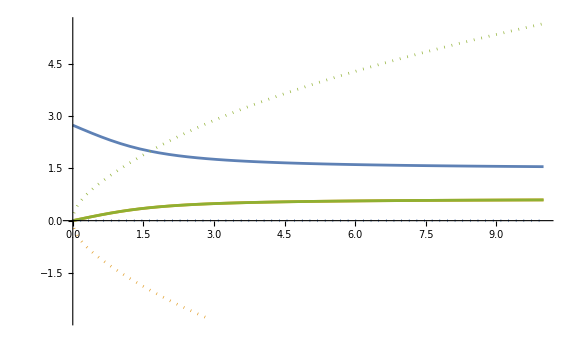

```mathematica
{
a(s-c),
b r-k c s,
s(r-1)
}
Solve[Map[#==0&,%],{r,c,s}]
Grad[%%,{r,c,s}];
%//MatrixForm
ReImPlot[Evaluate[%%/.%%%[[1]]/.{b->2.5,k->3}//Eigenvalues],{a,0,10}]
```